```mathematica
(*******************************************************electron in mp=207*)
SetDirectory[NotebookDirectory[]];
Clear[NUMdataHAR,NUMdataKIN,dataEXT,VARdataHAR,VARdataKIN,orbe,NUMdataCORR,NUMtotal,VARdataCORR,VARtotal,plot1,nn,plot2];

(* NUM *)
NUMdataHAR=ToExpression[Import["finalNUM_harE_207.txt","Lines"]];
NUMdataKIN=ToExpression[Import["finalNUM_kinE_207.txt","Lines"]];
dataEXT=ToExpression[Import["final_exE_207.txt","Lines"]];

(* VAR *)
VARdataHAR=ToExpression[Import["finalVAR_harE_207.txt","Lines"]];
VARdataKIN=ToExpression[Import["finalVAR_kinE_207.txt","Lines"]];
orbe=-0.43-0.06;

NUMdataCORR=Table[{dataEXT[[i,1]],orbe-dataEXT[[i,2]]-NUMdataKIN[[i,2]]-NUMdataHAR[[i,2]]},{i,Length[dataEXT]}];
NUMtotal=Table[{dataEXT[[i,1]],dataEXT[[i,2]]+NUMdataCORR[[i,2]]+NUMdataHAR[[i,2]]},{i,Length[dataEXT]}];

VARdataCORR=Table[{dataEXT[[i,1]],orbe-dataEXT[[i,2]]-VARdataKIN[[i,2]]-VARdataHAR[[i,2]]},{i,Length[dataEXT]}];
VARtotal=Table[{dataEXT[[i,1]],dataEXT[[i,2]]+VARdataCORR[[i,2]]+VARdataHAR[[i,2]]},{i,Length[dataEXT]}];
```

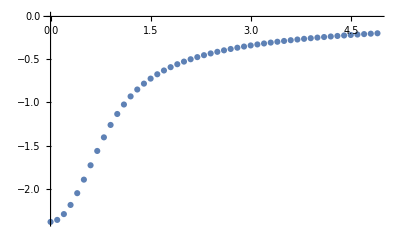

```mathematica
ListPlot[NUMtotal]
```

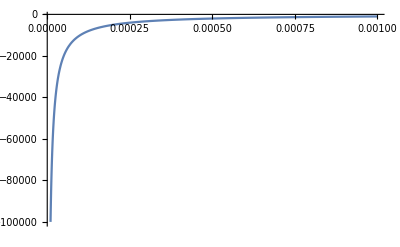

```mathematica
Plot[-1/x,{x,10^-5,0.001},PlotRange->All]
```

```mathematica
fit=NonlinearModelFit[NUMtotal,a1*Exp[-b1*x]+a2*Exp[-b2*x^2]+a3*Exp[-b3*x^3],{a1,b1,a2,b2,a3,b3},x]
```

FittedModel[-0.78967 ⅇ^(-0.288571 x)-2.67712 ⅇ^(-0.754074 x^2)+1.05852 ⅇ^(-0.391301 x^3)]

```mathematica
fit=NonlinearModelFit[NUMtotal,a1*Exp[-b1*x^2]+a2*Exp[-b2*x^2]+a3*Exp[-b3*x^2]+a4*Exp[-b4*x^2],{a1,b1,a2,b2,a3,b3,a4,b4},x]
```

FittedModel[-1.18282 ⅇ^(-1.69581 x^2)-0.60301 ⅇ^(-0.513736 x^2)-0.345017 ⅇ^(-0.132273 x^2)-0.258096 ⅇ^(-0.0147191 x^2)]

```mathematica
fit["RSquared"]
```

0.999821

```mathematica
fit["RSquared"]
```

1.

```mathematica
fit//Normal
```

-1.18282 ⅇ^(-1.69581 x^2)-0.60301 ⅇ^(-0.513736 x^2)-0.345017 ⅇ^(-0.132273 x^2)-0.258096 ⅇ^(-0.0147191 x^2)

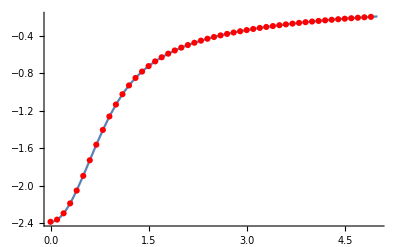

```mathematica
Show[{Plot[fit[x],{x,10^-10,5},PlotRange->All],ListPlot[NUMtotal,PlotStyle->Red]}]
```

```mathematica
Fit[NUMtotal,{a1*x,a2*x^2,a3*x^3},{a1,a2,a3}]
```

Fit[{{1.×10^-10,-2.38777},{0.1,-2.36457},{0.2,-2.29714},{0.3,-2.19081},{0.4,-2.0539},{0.5,-1.89661},{0.6,-1.72971},{0.7,-1.56318},{0.8,-1.40512},{0.9,-1.26098},{1.,-1.13355},{1.1,-1.02329},{1.2,-0.929099},{1.3,-0.849002},{1.4,-0.780786},{1.5,-0.722351},{1.6,-0.671893},{1.7,-0.627942},{1.8,-0.58933},{1.9,-0.55514},{2.,-0.524648},{2.1,-0.49728},{2.2,-0.472575},{2.3,-0.450157},{2.4,-0.429719},{2.5,-0.411008},{2.6,-0.39381},{2.7,-0.377947},{2.8,-0.363266},{2.9,-0.349639},{3.,-0.336954},{3.1,-0.325115},{3.2,-0.314038},{3.3,-0.30365},{3.4,-0.293888},{3.5,-0.284694},{3.6,-0.276021},{3.7,-0.267822},{3.8,-0.260059},{3.9,-0.252697},{4.,-0.245705},{4.1,-0.239053},{4.2,-0.232718},{4.3,-0.226674},{4.4,-0.220903},{4.5,-0.215384},{4.6,-0.2101},{4.7,-0.205036},{4.8,-0.200177},{4.9,-0.195511}},{a1 x,a2 x^2,a3 x^3},{a1,a2,a3}]

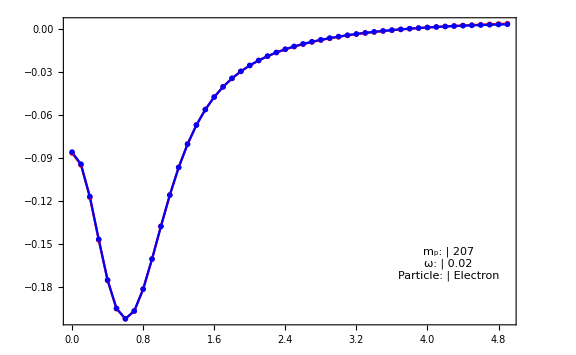

```mathematica
nn=TableForm[{{"m_p:","207"},{"ω:","0.02"},{"Particle:","Electron"}}];
plot11=ListLinePlot[{NUMdataCORR,VARdataCORR},Frame->True,PlotStyle->{Red,Blue,Black,Darker[Green]},PlotMarkers->{"OpenMarkers",4.8},PlotRange->All,ImageSize->Large,Epilog->Inset[Framed[nn],Scaled[{0.85,0.2}]]]
(*Export["plot_veffE_207.png",plot]*)
```

```mathematica
NUMdataCORR[[-1]]
```

{4.9,0.00376881}

```mathematica
Export["VARdataCORR_E_207.txt",VARdataCORR];
```

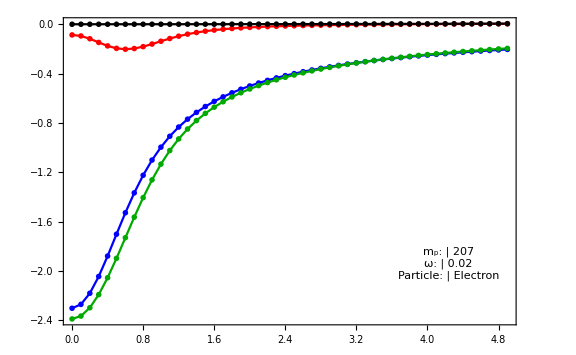

```mathematica
plot12=ListLinePlot[{NUMdataCORR,NUMdataHAR,dataEXT,NUMtotal},Frame->True,PlotStyle->{Red,Blue,Black,Darker[Green]},PlotMarkers->{"OpenMarkers",4.8},PlotRange->All,ImageSize->Large,Epilog->Inset[Framed[nn],Scaled[{0.85,0.2}]]]
```

```mathematica
(*******************************************************electron in mp=1836*)
SetDirectory[NotebookDirectory[]];
Clear[NUMdataHAR,NUMdataKIN,dataEXT,VARdataHAR,VARdataKIN,orbe,NUMdataCORR,NUMtotal,VARdataCORR,VARtotal,plot1,nn,plot2];

(* NUM *)
NUMdataHAR=ToExpression[Import["finalNUM_harE_1836.txt","Lines"]];
NUMdataKIN=ToExpression[Import["finalNUM_kinE_1836.txt","Lines"]];
dataEXT=ToExpression[Import["final_exE_1836.txt","Lines"]];

(* VAR *)
VARdataHAR=ToExpression[Import["finalVAR_harE_1836.txt","Lines"]];
VARdataKIN=ToExpression[Import["finalVAR_kinE_1836.txt","Lines"]];
orbe=-0.43-0.065;

NUMdataCORR=Table[{dataEXT[[i,1]],orbe-dataEXT[[i,2]]-NUMdataKIN[[i,2]]-NUMdataHAR[[i,2]]},{i,Length[dataEXT]}];
NUMtotal=Table[{dataEXT[[i,1]],dataEXT[[i,2]]+NUMdataCORR[[i,2]]+NUMdataHAR[[i,2]]},{i,Length[dataEXT]}];

VARdataCORR=Table[{dataEXT[[i,1]],orbe-dataEXT[[i,2]]-VARdataKIN[[i,2]]-VARdataHAR[[i,2]]},{i,Length[dataEXT]}];
VARtotal=Table[{dataEXT[[i,1]],dataEXT[[i,2]]+VARdataCORR[[i,2]]+VARdataHAR[[i,2]]},{i,Length[dataEXT]}];
```

```mathematica
fit=NonlinearModelFit[NUMtotal,a1*Exp[-b1*x^2]+a2*Exp[-b2*x^2]+a3*Exp[-b3*x^2]+a4*Exp[-b4*x^2],{a1,b1,a2,b2,a3,b3,a4,b4},x]
```

FittedModel[-2.36917 ⅇ^(-9.06431 x^2)-1.43891 ⅇ^(-2.17542 x^2)-0.683618 ⅇ^(-0.389348 x^2)-0.407959 ⅇ^(-0.031088 x^2)]

```mathematica
fit["RSquared"]
```

0.999995

```mathematica
fit//Normal
```

-2.36917 ⅇ^(-9.06431 x^2)-1.43891 ⅇ^(-2.17542 x^2)-0.683618 ⅇ^(-0.389348 x^2)-0.407959 ⅇ^(-0.031088 x^2)

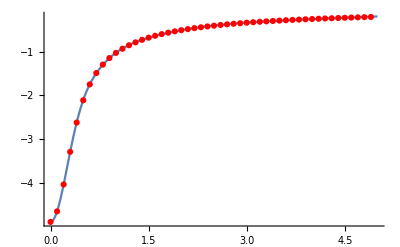

```mathematica
Show[{Plot[fit[x],{x,10^-10,5},PlotRange->All],ListPlot[NUMtotal,PlotStyle->Red]}]
```

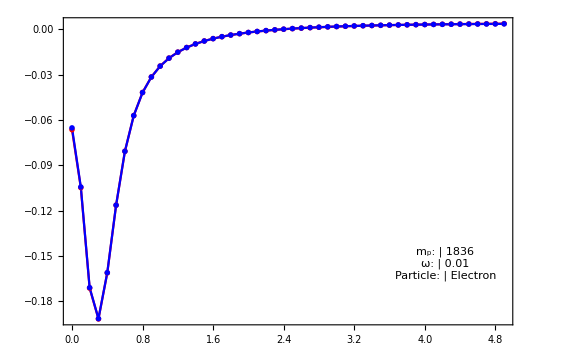

```mathematica
nn=TableForm[{{"m_p:","1836"},{"ω:","0.01"},{"Particle:","Electron"}}];
plot21=ListLinePlot[{NUMdataCORR,VARdataCORR},Frame->True,PlotStyle->{Red,Blue,Black,Darker[Green]},PlotMarkers->{"OpenMarkers",4.8},PlotRange->All,ImageSize->Large,Epilog->Inset[Framed[nn],Scaled[{0.85,0.2}]]]
(*Export["plot_veffE_207.png",plot]*)
```

```mathematica
NUMdataCORR[[-1]]
```

{4.9,0.00368169}

```mathematica
Export["VARdataCORR_E_1836.txt",VARdataCORR];
```

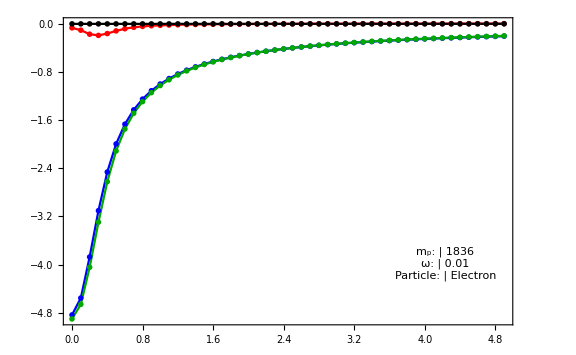

```mathematica
plot22=ListLinePlot[{NUMdataCORR,NUMdataHAR,dataEXT,NUMtotal},Frame->True,PlotStyle->{Red,Blue,Black,Darker[Green]},PlotMarkers->{"OpenMarkers",4.8},PlotRange->All,ImageSize->Large,Epilog->Inset[Framed[nn],Scaled[{0.85,0.2}]]]
```

```mathematica
(*******************************************************PC in mp=207*)
SetDirectory[NotebookDirectory[]];
Clear[NUMdataHAR,NUMdataKIN,dataEXT,VARdataHAR,VARdataKIN,orbe,NUMdataCORR,NUMtotal,VARdataCORR,VARtotal,plot1,nn,plot2];

(* NUM *)
NUMdataHAR=ToExpression[Import["finalNUM_harP_207.txt","Lines"]];
NUMdataKIN=ToExpression[Import["finalNUM_kinP_207.txt","Lines"]];
dataEXT=ToExpression[Import["final_exP_207.txt","Lines"]];

(* VAR *)
VARdataHAR=ToExpression[Import["finalVAR_harP_207.txt","Lines"]];
VARdataKIN=ToExpression[Import["finalVAR_kinP_207.txt","Lines"]];
orbe=0.03;

NUMdataCORR=Table[{dataEXT[[i,1]],orbe-dataEXT[[i,2]]-NUMdataKIN[[i,2]]-NUMdataHAR[[i,2]]},{i,Length[dataEXT]}];
NUMtotal=Table[{dataEXT[[i,1]],dataEXT[[i,2]]+NUMdataCORR[[i,2]]+NUMdataHAR[[i,2]]},{i,Length[dataEXT]}];

VARdataCORR=Table[{dataEXT[[i,1]],orbe-dataEXT[[i,2]]-VARdataKIN[[i,2]]-VARdataHAR[[i,2]]},{i,Length[dataEXT]}];
VARtotal=Table[{dataEXT[[i,1]],dataEXT[[i,2]]+VARdataCORR[[i,2]]+VARdataHAR[[i,2]]},{i,Length[dataEXT]}];
```

```mathematica
fit=NonlinearModelFit[NUMtotal,a1*Exp[-b1*x^2]+a2*Exp[-b2*x^2]+a3*Exp[-b3*x^2]+a4*Exp[-b4*x^2],{a1,b1,a2,b2,a3,b3,a4,b4},x]
```

FittedModel[-0.0502362 ⅇ^(-0.161107 x^2)-0.0521655 ⅇ^(-0.154941 x^2)-0.0514286 ⅇ^(-0.151237 x^2)+0.15353 ⅇ^(0.122082 x^2)]

```mathematica
fit=NonlinearModelFit[NUMtotal,a1*Exp[-b1*x^2]+a2*Exp[-b2*x^2],{a1,b1,a2,b2},x]
```

FittedModel[-0.37303 ⅇ^(-0.0590131 x^2)+0.372863 ⅇ^(0.0534262 x^2)]

```mathematica
fit["RSquared"]
```

1.

```mathematica
fit["RSquared"]
```

0.999996

```mathematica
fit//Normal
```

-0.37303 ⅇ^(-0.0590131 x^2)+0.372863 ⅇ^(0.0534262 x^2)

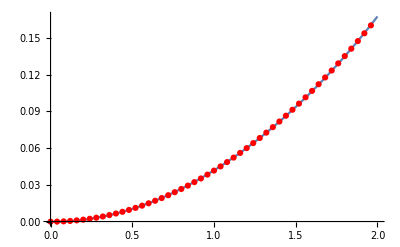

```mathematica
Show[{Plot[fit[x],{x,10^-10,2},PlotRange->All],ListPlot[NUMtotal,PlotStyle->Red]}]
```

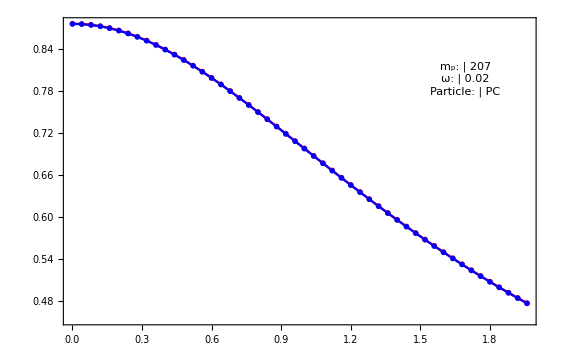

```mathematica
nn=TableForm[{{"m_p:","207"},{"ω:","0.02"},{"Particle:","PC"}}];
plot31=ListLinePlot[{NUMdataCORR,VARdataCORR},Frame->True,PlotStyle->{Red,Blue,Black,Darker[Green]},PlotMarkers->{"OpenMarkers",4.8},PlotRange->All,ImageSize->Large,Epilog->Inset[Framed[nn],Scaled[{0.85,0.8}]]]
(*Export["plot_veffE_207.png",plot]*)
```

```mathematica
Export["VARdataCORR_P_207.txt",VARdataCORR];
```

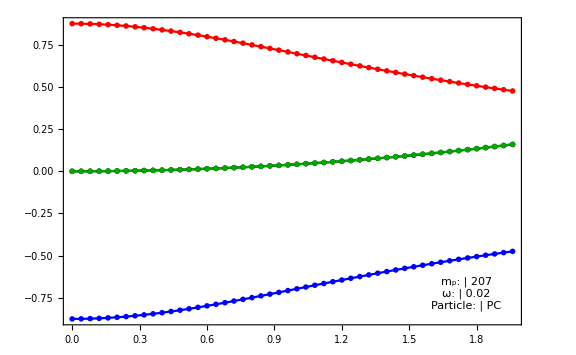

```mathematica
plot32=ListLinePlot[{NUMdataCORR,NUMdataHAR,dataEXT,NUMtotal},Frame->True,PlotStyle->{Red,Blue,Black,Darker[Green]},PlotMarkers->{"OpenMarkers",4.8},PlotRange->All,ImageSize->Large,Epilog->Inset[Framed[nn],Scaled[{0.88,0.1}]]]
```

```mathematica
(*******************************************************PC in mp=1836*)
SetDirectory[NotebookDirectory[]];
Clear[NUMdataHAR,NUMdataKIN,dataEXT,VARdataHAR,VARdataKIN,orbe,NUMdataCORR,NUMtotal,VARdataCORR,VARtotal,plot1,nn,plot2];

(* NUM *)
NUMdataHAR=ToExpression[Import["finalNUM_harP_1836.txt","Lines"]];
NUMdataKIN=ToExpression[Import["finalNUM_kinP_1836.txt","Lines"]];
dataEXT=ToExpression[Import["final_exP_1836.txt","Lines"]];

(* VAR *)
VARdataHAR=ToExpression[Import["finalVAR_harP_1836.txt","Lines"]];
VARdataKIN=ToExpression[Import["finalVAR_kinP_1836.txt","Lines"]];
orbe=0.015;

NUMdataCORR=Table[{dataEXT[[i,1]],orbe-dataEXT[[i,2]]-NUMdataKIN[[i,2]]-NUMdataHAR[[i,2]]},{i,Length[dataEXT]}];
NUMtotal=Table[{dataEXT[[i,1]],dataEXT[[i,2]]+NUMdataCORR[[i,2]]+NUMdataHAR[[i,2]]},{i,Length[dataEXT]}];

VARdataCORR=Table[{dataEXT[[i,1]],orbe-dataEXT[[i,2]]-VARdataKIN[[i,2]]-VARdataHAR[[i,2]]},{i,Length[dataEXT]}];
VARtotal=Table[{dataEXT[[i,1]],dataEXT[[i,2]]+VARdataCORR[[i,2]]+VARdataHAR[[i,2]]},{i,Length[dataEXT]}];
```

```mathematica
fit=NonlinearModelFit[NUMtotal,a1*Exp[-b1*x^2]+a2*Exp[-b2*x^2]+a3*Exp[-b3*x^2]+a4*Exp[-b4*x^2],{a1,b1,a2,b2,a3,b3,a4,b4},x]
```

FittedModel[-0.0707831 ⅇ^(-0.280616 x^2)-0.0644909 ⅇ^(-0.280392 x^2)-0.0733086 ⅇ^(-0.280117 x^2)+0.207641 ⅇ^(0.187533 x^2)]

```mathematica
fit=NonlinearModelFit[NUMtotal,a1*Exp[-b1*x^2]+a2*Exp[-b2*x^2],{a1,b1,a2,b2},x]
```

FittedModel[-0.905641 ⅇ^(-0.0531794 x^2)+0.905584 ⅇ^(0.0485919 x^2)]

```mathematica
fit["RSquared"]
```

1.

```mathematica
fit//Normal
```

-0.905641 ⅇ^(-0.0531794 x^2)+0.905584 ⅇ^(0.0485919 x^2)

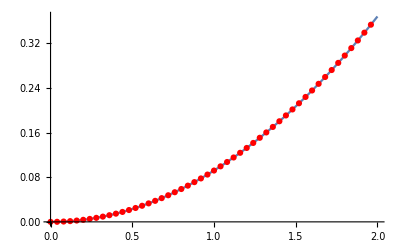

```mathematica
Show[{Plot[fit[x],{x,10^-10,2},PlotRange->All],ListPlot[NUMtotal,PlotStyle->Red]}]
```

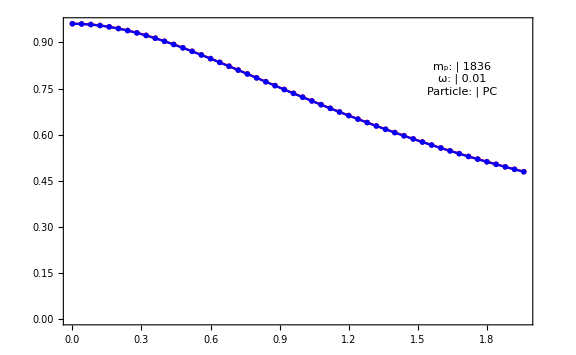

```mathematica
nn=TableForm[{{"m_p:","1836"},{"ω:","0.01"},{"Particle:","PC"}}];
plot41=ListLinePlot[{NUMdataCORR,VARdataCORR},Frame->True,PlotStyle->{Red,Blue,Black,Darker[Green]},PlotMarkers->{"OpenMarkers",4.8},PlotRange->All,ImageSize->Large,Epilog->Inset[Framed[nn],Scaled[{0.85,0.8}]]]
(*Export["plot_veffE_207.png",plot]*)
```

```mathematica
Export["VARdataCORR_P_1836.txt",VARdataCORR];
```

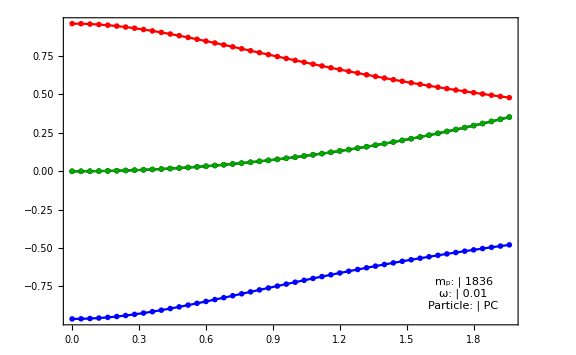

```mathematica
plot42=ListLinePlot[{NUMdataCORR,NUMdataHAR,dataEXT,NUMtotal},Frame->True,PlotStyle->{Red,Blue,Black,Darker[Green]},PlotMarkers->{"OpenMarkers",4.8},PlotRange->All,ImageSize->Large,Epilog->Inset[Framed[nn],Scaled[{0.88,0.1}]]]
```

```mathematica
(* Grids*)
```

```mathematica
leg1=LineLegend[{Directive[PointSize[1/72],AbsoluteThickness[1.6],Red],Directive[PointSize[1/72],AbsoluteThickness[1.6],Blue]},{"Numerical Correlation Potential","Variational Correlation Potential"},LegendMarkers->{{Graphics[{{White,Disk[{0,0},Offset[{2.4,2.4},{0.,0.}]]},{AbsoluteThickness[1.2],Dashing[{}],Circle[{0,0},Offset[{2.4,2.4},{0.,0.}]]}}],7.800000000000001},{Graphics[{{White,Polygon[{Offset[{0,3.1999999999999997}],Offset[{-2.7712812921102032,-1.5999999999999999}],Offset[{2.7712812921102032,-1.5999999999999999}]}]},{AbsoluteThickness[1.2],Dashing[{}],JoinedCurve[Line[{Offset[{0,3.1999999999999997}],Offset[{-2.7712812921102032,-1.5999999999999999}],Offset[{2.7712812921102032,-1.5999999999999999}],Offset[{0,3.1999999999999997}]}],CurveClosed->True]}}],7.800000000000001}},Joined->{True,True},LegendLayout->"Row",ImageSize->{500,30}]
```

```mathematica
leg2=LineLegend[{Directive[PointSize[1/72],AbsoluteThickness[1.6],Red],Directive[PointSize[1/72],AbsoluteThickness[1.6],Blue],Directive[PointSize[1/72],AbsoluteThickness[1.6],Black],Directive[PointSize[1/72],AbsoluteThickness[1.6],RGBColor[0,2/3,0]]},{"Correlation Pot","Hartree Pot","External Pot","Total Pot=ex+har+corr"},LegendMarkers->{{Graphics[{{White,Disk[{0,0},Offset[{2.4,2.4},{0.,0.}]]},{AbsoluteThickness[1.2],Dashing[{}],Circle[{0,0},Offset[{2.4,2.4},{0.,0.}]]}}],7.800000000000001},{Graphics[{{White,Polygon[{Offset[{0,3.1999999999999997}],Offset[{-2.7712812921102032,-1.5999999999999999}],Offset[{2.7712812921102032,-1.5999999999999999}]}]},{AbsoluteThickness[1.2],Dashing[{}],JoinedCurve[Line[{Offset[{0,3.1999999999999997}],Offset[{-2.7712812921102032,-1.5999999999999999}],Offset[{2.7712812921102032,-1.5999999999999999}],Offset[{0,3.1999999999999997}]}],CurveClosed->True]}}],7.800000000000001},{Graphics[{{White,Polygon[{Offset[{0,2.9999999999999996}],Offset[{2.9999999999999996,0}],Offset[{0,-2.9999999999999996}],Offset[{-2.9999999999999996,0}]}]},{AbsoluteThickness[1.2],Dashing[{}],Line[{Offset[{0,2.9999999999999996}],Offset[{2.9999999999999996,0}],Offset[{0,-2.9999999999999996}],Offset[{-2.9999999999999996,0}],Offset[{0,2.9999999999999996}]}]}}],7.800000000000001},{Graphics[{{White,Polygon[{Offset[{-2.1999999999999997,-2.1999999999999997}],Offset[{2.1999999999999997,-2.1999999999999997}],Offset[{2.1999999999999997,2.1999999999999997}],Offset[{-2.1999999999999997,2.1999999999999997}],Offset[{-2.1999999999999997,-2.1999999999999997}]}]},{AbsoluteThickness[1.2],Dashing[{}],Line[{Offset[{-2.1999999999999997,-2.1999999999999997}],Offset[{2.1999999999999997,-2.1999999999999997}],Offset[{2.1999999999999997,2.1999999999999997}],Offset[{-2.1999999999999997,2.1999999999999997}],Offset[{-2.1999999999999997,-2.1999999999999997}]}]}}],7.800000000000001}},Joined->{True,True,True,True},LegendLayout->"Row",ImageSize->{500,30}]
```

```mathematica
grid01=Grid[{{plot11,plot21},{plot31,plot41}}];
grid02=Grid[{{plot12,plot22},{plot32,plot42}}];
```

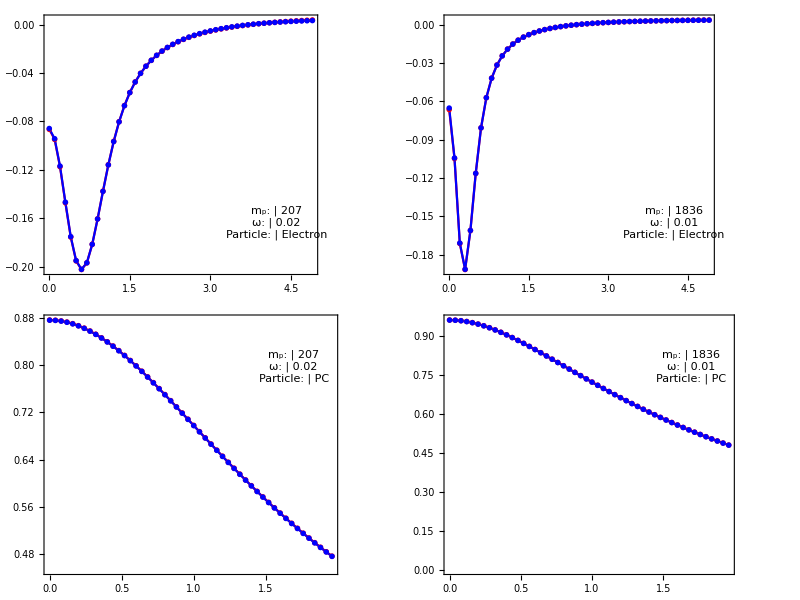

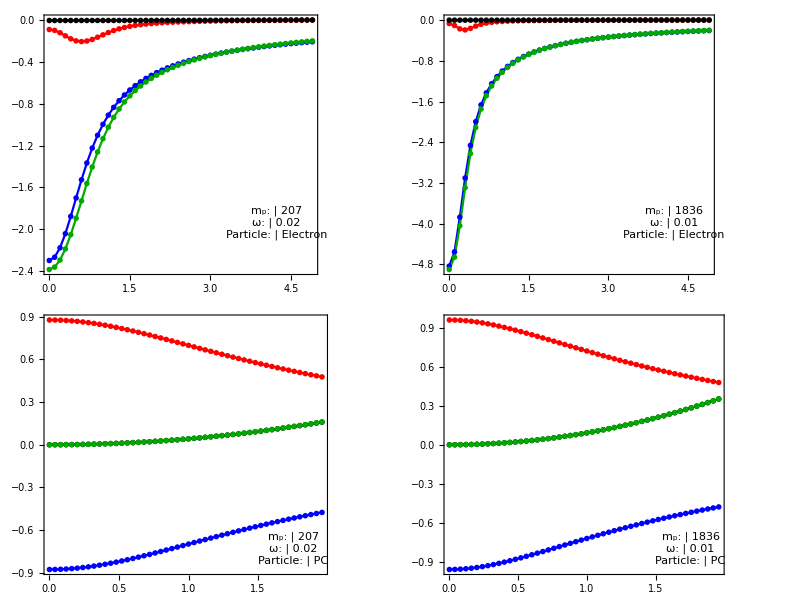

```mathematica
grid1=Grid[{{grid01},{leg1}},Alignment->Center]
grid2=Grid[{{grid02},{leg2}},Alignment->Center]
```

```mathematica
Export["grid1_NUM_vs_VAR.png",grid1]
Export["grid2_veff_coms.png",grid2]
```

grid1_NUM_vs_VAR.png

grid2_veff_coms.png